# Machine Learning I

#### Jesse Galef - jesseg@wolfram.com

```mathematica
-Graphics-       -Graphics-
```

## What Machine Learning Is and Isn’t

## Machine Learning Is:

Finding patterns in data

Solving your problem in an underspecified way

Often impressive and powerful

```mathematica
-Graphics--Graphics-
```

## Machine Learning Is Not:

Magic

A mind reader

### Machine Learning Solves What You Asks (Not What You Want):

Evolved algorithm for landing aircraft exploited overflow errors in the physics simulator by creating large forces that were estimated to be zero, resulting in a perfect score
Feldt, 1998 	Generating diverse software versions with genetic programming : An experimental study.

Neural nets evolved to classify edible and poisonous mushrooms took advantage of the data being presented 
in alternating order, and didn’t actually learn any features of the input images
Ellefsen et al, 2015 	Neural modularity helps organisms evolve to learn new skills without forgetting old skills

Deep learning model to detect pneumonia in chest x-rays worked out which x-ray machine was used to take the picture; 
certain x-ray machines (and hospital sites) are used for sicker patients.
Zech et al, 2018		Variable generalization performance of a deep learning model to detect pneumonia in chest radiographs: A cross-sectional study

Genetic algorithm is supposed to configure a circuit into an oscillator, but instead makes a radio to pick up signals from neighboring computers
Bird & Layzell, 2002	The Evolved Radio and its Implications for Modelling the Evolution of Novel Sensors

## What kind of ML can you do in Mathematica?

## Does your data come with labeled answers?

### Yes, my data is labeled: Supervised Learning

Classifying an example into known categories

Predicting a value

Wolfram Language functions, cleverly named:

Classify

Predict

### No, my data does not come with labeled answers: Unsupervised Learning

Modeling and representing the data itself

ClusterClassify, FindClusters

AnomalyDetection

LearnDistribution

SynthesizeMissingValues

DimensionReduction, FeatureExtraction

```mathematica
colorclusters=FindClusters[RandomColor[100]]
```

{{RGBColor[0.605687779273459, 0.2616387967763629, 0.36780690096285507],RGBColor[0.3173216571241191, 0.14542737107868886, 0.0948580944895625],RGBColor[0.6959676380883153, 0.10514695919927308, 0.377482263727581],RGBColor[0.8869874832821079, 0.009390115280555333, 0.15444936333656112],RGBColor[0.415934691365897, 0.22209266140634343, 0.22373741002388026],RGBColor[0.8685059232011636, 0.14642245347550875, 0.5195563577724518],RGBColor[0.8169594565651523, 0.23750230018506802, 0.0698271847684171],RGBColor[0.9738745208964925, 0.46585066285537646, 0.39999844193338974],RGBColor[0.8066075047855157, 0.096990942702887, 0.2516530465267859],RGBColor[0.9247016073181054, 0.1897165817229125, 0.2215751558882555],RGBColor[0.6875014408940614, 0.28232864463109175, 0.05170194185255328],RGBColor[0.9699658640946529, 0.537392216805169, 0.6303071730361789],RGBColor[0.8258814130391161, 0.4281175414382181, 0.25653445974015954],RGBColor[0.9128662290772187, 0.29523033451758596, 0.4197581027791577],RGBColor[0.9186132035254024, 0.00486938111290014, 0.5090292869630353],RGBColor[0.34718790419853973, 0.07441394813784141, 0.11483794218783694],RGBColor[0.6577470147075029, 0.07484149227664294, 0.2800620063137984]},{RGBColor[0.7104354557136341, 0.48211982763289263, 0.5911753091697804],RGBColor[0.8699580972089878, 0.6238285106578139, 0.9220083970137032],RGBColor[0.8172430216280664, 0.5487374787670767, 0.9709444479966323],RGBColor[0.691463349839722, 0.5381956500265634, 0.944618833613323]},{RGBColor[0.5722606046964946, 0.8534177189897965, 0.01795938596807689],RGBColor[0.31235451551571947, 0.828660608064985, 0.2973936057511881],RGBColor[0.9012451709628488, 0.4812455559004043, 0.495287616155091],RGBColor[0.860647898834322, 0.784440934151305, 0.1970945640877768],RGBColor[0.5521918773395129, 0.7882538509151988, 0.17082306997225327],RGBColor[0.025778287110469478, 0.4075813668309798, 0.4038912153955707],RGBColor[0.17569591370620263, 0.4363672593362955, 0.54477663072964],RGBColor[0.7496004389818325, 0.6642695215968124, 0.3484331692516074],RGBColor[0.23970175616197453, 0.9311638954157317, 0.7521264778763022],RGBColor[0.4508842306997394, 0.6363971109868336, 0.6080791072159499],RGBColor[0.031978369357108294, 0.8463892201449259, 0.5054858777253253],RGBColor[0.2728470908610463, 0.23782794336061808, 0.41347632440479654],RGBColor[0.8288835682605429, 0.9286693407805153, 0.777475072576475],RGBColor[0.5872905949574283, 0.7954473348886488, 0.26507811014951277],RGBColor[0.5938547761825999, 0.7076634040425662, 0.6022546834255544],RGBColor[0.1999691182212613, 0.8021863880880744, 0.7721909885281997],RGBColor[0.35669649198215536, 0.6903460011766596, 0.03151706058939041],RGBColor[0.020899702456671054, 0.624324892550622, 0.9064891297083923],RGBColor[0.7292107293482717, 0.770153023128404, 0.5648618965428542],RGBColor[0.24639069682084047, 0.4455279631289635, 0.6870234102779644],RGBColor[0.48227703741391026, 0.9473084914320571, 0.6873587269960291],RGBColor[0.017445690085010623, 0.5989675454647048, 0.052463190979954666],RGBColor[0.46918958455181525, 0.4892662983441529, 0.5272093669895235],RGBColor[0.4077852205973249, 0.3921675494667798, 0.5620757734615991],RGBColor[0.9074872841042898, 0.7853473662347059, 0.6787907517424967],RGBColor[0.3592450495964936, 0.965491618211838, 0.574446964964398],RGBColor[0.4668011088964108, 0.6861110803466419, 0.5692340976190826],RGBColor[0.24811656772240842, 0.36669532676089167, 0.7527969154336736],RGBColor[0.16740405082809695, 0.7386214112280489, 0.6365602617766866],RGBColor[0.2715529754326427, 0.986402509113407, 0.11728987975495686],RGBColor[0.42493816734942147, 0.7008740700851124, 0.5295681570574808],RGBColor[0.7659216447646846, 0.7284713061008683, 0.7247222977062009],RGBColor[0.03983953305288268, 0.6676103359761958, 0.827483893651886],RGBColor[0.27981355065965197, 0.8559770908495214, 0.6435242186647285],RGBColor[0.8126914061581705, 0.9336792078683853, 0.41862256956177113],RGBColor[0.8472653169341444, 0.8245255335216435, 0.18229019104767952],RGBColor[0.5726905706005858, 0.869322006124086, 0.6183878130884073],RGBColor[0.531029802348042, 0.8539541091485265, 0.1456264430336749],RGBColor[0.36423988524739426, 0.9902943619013616, 0.037450808474429165],RGBColor[0.3446265121577643, 0.561862408903596, 0.4545601146969598],RGBColor[0.8429811541992642, 0.6126853486052939, 0.2812358878789214],RGBColor[0.6916074201819047, 0.7870130846347796, 0.47829466309052315],RGBColor[0.27536767476887647, 0.27204934596171104, 0.5358961410141929],RGBColor[0.7414385322802926, 0.6011388558213397, 0.39140742012521845],RGBColor[0.4784726752610984, 0.5694705658571562, 0.8098932335157734],RGBColor[0.6885796581722228, 0.6271234222941859, 0.2068264413491756],RGBColor[0.1834235514062883, 0.3784616118115922, 0.48570924192243536],RGBColor[0.3320617402312236, 0.39355682674929193, 0.8016278154241336],RGBColor[0.22465623545165592, 0.9492045345936349, 0.5599519363766634],RGBColor[0.17222162182374423, 0.4816734696510918, 0.9112500504560994]},{RGBColor[0.29112144194469947, 0.05813288295279695, 0.5969144468348129],RGBColor[0.44138104239083886, 0.21873575632896536, 0.7102911522389528],RGBColor[0.41432022586906014, 0.11421998705711922, 0.6600611560189653],RGBColor[0.05158706484788689, 0.1423686012328993, 0.6537586721169004],RGBColor[0.4856942678717666, 0.23397117224388952, 0.808823289729041],RGBColor[0.11947827097188046, 0.08100301465731197, 0.9638689005084351],RGBColor[0.7040597242082385, 0.27266563993974047, 0.9376107549290018],RGBColor[0.19724603129157336, 0.06069028326732373, 0.42227940048322266],RGBColor[0.5595447109313456, 0.18193764117231037, 0.7841791370805735],RGBColor[0.5848115786565147, 0.1439005248501115, 0.5436654631562301],RGBColor[0.06135572243381615, 0.12118431779512617, 0.7131890885239833],RGBColor[0.23284252938995897, 0.15281485851723775, 0.7147377668233161],RGBColor[0.6898639163227469, 0.12000800733234374, 0.7202229092103851],RGBColor[0.32070511281366776, 0.08473232390272778, 0.7897431486348396],RGBColor[0.5252119112815821, 0.04328359827808459, 0.8998629192959564],RGBColor[0.2022728564795493, 0.3305781508646053, 0.9223867868722784],RGBColor[0.8345781524589218, 0.1569246058273588, 0.9841912026419735],RGBColor[0.9362750025248945, 0.0021989942474474056, 0.8386660718884296],RGBColor[0.7699666431576746, 0.05807564152565692, 0.9887325560074733],RGBColor[0.7373779972880854, 0.26211563434005636, 0.7492926613782824],RGBColor[0.462827131007135, 0.12388650700353532, 0.5737743095964836],RGBColor[0.6042796129728352, 0.2193645448338304, 0.8187778524754383]},{RGBColor[0.03875466407856498, 0.27202309071330255, 0.00641383679499663],RGBColor[0.5460307789311778, 0.3838550348839598, 0.14507469332070433],RGBColor[0.42221297374369904, 0.40390117165935724, 0.2024191617883131],RGBColor[0.4042089398199389, 0.3726375598709333, 0.040017508728299234],RGBColor[0.3086581956652903, 0.3600124562689566, 0.10560222116813867],RGBColor[0.4687516970543124, 0.4693929249673292, 0.1671009132701946],RGBColor[0.12109726466851112, 0.34751609537087225, 0.05541814019260016]}}

```mathematica
colordistribution=LearnDistribution[colorclusters[[2]]];
RandomVariate[colordistribution,20]
```

{RGBColor[1.0055456382541044, 0.5611018017153077, 0.9889731633197163],RGBColor[0.8211283126115411, 0.4362217515782073, 0.4749263473068177],RGBColor[0.7231174539138264, 0.5029130803191426, 0.8682112869446071],RGBColor[0.7467551212691542, 0.5495125054098543, 0.9850155083907862],RGBColor[0.7492434975868655, 0.49895155447273254, 1.1306198600592272],RGBColor[0.6774182353078426, 0.5600874028554389, 1.1519943135663213],RGBColor[0.5965284872032165, 0.5252001717455752, 1.0974652147605022],RGBColor[0.7426699036579645, 0.5753150864219605, 1.1075187012156777],RGBColor[0.5942021383067644, 0.5572370734860509, 0.7847814892076408],RGBColor[0.8124844411474597, 0.4725059186208325, 0.9932383903224892],RGBColor[0.7666987062396421, 0.523536037442382, 0.5078554008402001],RGBColor[0.7071230643367505, 0.5897967610116549, 1.179932497319041],RGBColor[0.6700405021228379, 0.5713946238925299, 0.41946509677630417],RGBColor[0.6543528608145646, 0.5227484380318091, 0.5031049530253635],RGBColor[0.7892094423695715, 0.6188310034929349, 0.997745487057873],RGBColor[0.9465106175437104, 0.6325823304762935, 1.0976663012573162],RGBColor[0.8295926524226575, 0.5444834409009309, 0.3633096665146304],RGBColor[0.6759432915917994, 0.5563204912898195, 1.0523436582702825],RGBColor[0.7296184355430726, 0.4481059491147128, 0.5934776027734576],RGBColor[0.78089369181973, 0.46933644775468286, 0.6886920218100894]}

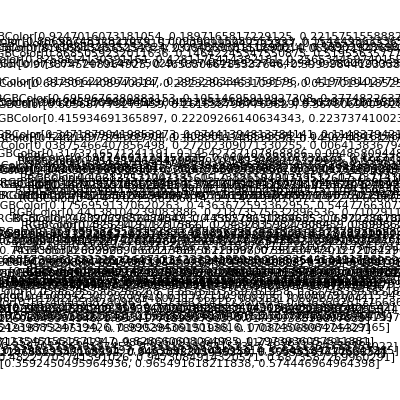

```mathematica
FeatureSpacePlot[Flatten[colorclusters]]
```

### Well...Sort of: Reinforcement learning

Active agent, feedback from environment

Wolfram Language functions:

BayesianMinimization

ActiveClassification, ActivePrediction

## Built-in Machine Learning Models in Mathematica

#### Pre-trained neural networks (NetModel)

```mathematica
SeedRandom[42];
mnist=ResourceData["MNIST"];
mnist[[;;10,1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
digitIdentifier=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

```mathematica
digitIdentifier[mnist[[1,1]],"Probabilities"]
```

<|0→1.,1→4.84591×10^-24,2→2.51356×10^-19,3→1.21359×10^-21,4→9.59967×10^-17,5→2.12143×10^-20,6→5.54537×10^-16,7→5.54455×10^-21,8→3.12773×10^-19,9→2.75405×10^-13|>

### Built-in Text Classifiers

```mathematica
lang=Classify["Language"]
```

ClassifierFunction[…]

```mathematica
lang["what is this?"]
```

English

```mathematica
lang["quelle langue est-ca?"]
```

French

```mathematica
lang["Marseille"]
```

French

```mathematica
lang["Beijing"]
```

English

```mathematica
DynamicModule[{x=""},
Column[{
InputField[Dynamic[x], String, ContinuousAction->True],Dynamic[Column@Classify["Language",x,"TopProbabilities"->3]]
}]]
```

```mathematica
DynamicModule[{x=""},
Column[{
InputField[Dynamic[x], String, ContinuousAction->True],Dynamic[Column@Classify["FacebookTopic",x,"TopProbabilities"->3]]
}]]
```

### Image Identify

```mathematica
ImageIdentify[{-Graphics-,-Graphics-}]
```

{domestic cat,domestic cat}

```mathematica
ImageIdentify[-Graphics-]
```

challah

```mathematica
NetModel["Wolfram ImageIdentify Net V1"]
```

NetChain[<>]

### TextStructure

```mathematica
TextStructure["The quick brown fox jumped over the lazy dog."]
```

The
Determinerquick
Adjectivebrown
Adjectivefox
Noun
Noun Phrase  jumped
Verb  over
Preposition  the
Determinerlazy
Adjectivedog
Noun
Noun Phrase
Prepositional Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
Classify& Predict Methods
```

There are many different algorithms and methods you can use:

Linear Models

e.g. Linear Regression, Logistic Regression

Each feature has a linear impact on the output, positive or negative (or zero)

Non-linear Models

e.g. Decision Trees, Nearest Neighbors, Random Forest, Boosted Trees

Can generate non-linear relationships between inputs and outputs

You can always read more about them in documentation!

### Classify Methods:

```mathematica
Predict Methods:
```

## Machine Learning Principles

#### Let’s take a single feature from the Boston Homes dataset (real data)

```mathematica
ExampleData[{"MachineLearning", "BostonHomes"}, "LongDescription"]
```

Home values for 506 Boston suburbs with potential influential factors (such as the crime rate, number of rooms, distance to employment centers, etc.).

	The test and training sets were obtained by creating a random sample of 30% of the data for the test set, using the rest for training.

```mathematica
features=First[ExampleData[{"MachineLearning", "BostonHomes"}, "VariableDescriptions"]];
Column[features]
```

Per capita crime rate by town
Proportion of residential land zoned for lots over 25000 square feet
Proportion of non-retail business acres per town
Charles River dummy variable (1 if tract bounds river, 0 otherwise)
Nitrogen oxide concentration (parts per 10 million)
Average number of rooms per dwelling
Proportion of owner-occupied units built prior to 1940
Weighted mean of distances to five Boston employment centers
Index of accessibility to radial highways
Full-value property-tax rater per $10000
Pupil-teacher ratio by town
1000(Bk-0.63)^2 where Bk is the proportion of Black or African-American residents by town
Lower status of the population (percent)
Median value of owner-occupied homes in $1000s

```mathematica
RandomSeed[42];
train=RandomSample[ExampleData[{"MachineLearning", "BostonHomes"}, "TrainingData"],150];
train={train[[All,1,8]],train[[All,2]]};

test=ExampleData[{"MachineLearning", "BostonHomes"}, "TestData"];
test={test[[All,1,8]],test[[All,2]]};
```

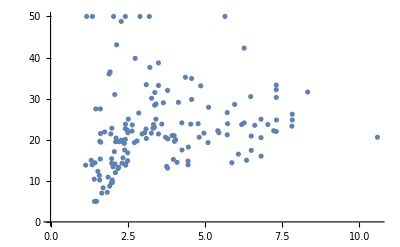

```mathematica
ListPlot[Transpose@train]
```

## Analytic approach

### Let’s find m and b for y = mx + b Minimizing the mean square error

```mathematica
meanSquareError[model_, {x_,y_}]:=Mean[(y-model[x])^2];
```

```mathematica
plotFit[{xvals_,yvals_}, f_]:=Labeled[Show[{
ListPlot[Transpose[{xvals,yvals}]],
Plot[f[xvalue],{xvalue,Sequence@@MinMax[xvals]},PlotRange->Automatic]}, PlotLabel->f[x]]
,
 "Mean Square Error: "<>ToString[meanSquareError[f, {xvals,yvals}]]
];
```

```mathematica
Manipulate[plotFit[train, (slope*#+intercept)&], {slope, 0,5}, {intercept, 5, 40}]
```

## Analytic Best Solution

```mathematica
loss = meanSquareError[intercept+#*slope&, train]
```

1/150 ((20.6-intercept-10.5857 slope)^2+(31.6-intercept-8.3248 slope)^2+(24.8-intercept-7.8278 slope)^2+(26.2-intercept-7.8265 slope)^2+(23.3-intercept-7.8148 slope)^2+(24.8-intercept-7.3172 slope)^2+(30.3-intercept-7.309 slope)^2+(33.3-intercept-7.309 slope)^2+(22-intercept-7.3073 slope)^2+(32.2-intercept-7.3073 slope)^2+(22.2-intercept-7.2255 slope)^2+(23.7-intercept-7.0355 slope)^2+(16-intercept-6.8185 slope)^2+(20.5-intercept-6.8147 slope)^2+(25-intercept-6.8147 slope)^2+(23.5-intercept-6.6115 slope)^2+(17.4-intercept-6.498 slope)^2+(20.9-intercept-6.498 slope)^2+(30.5-intercept-6.4798 slope)^2+(15-intercept-6.3467 slope)^2+(24.1-intercept-6.27 slope)^2+(42.3-intercept-6.27 slope)^2+(23.7-intercept-6.1899 slope)^2+(16.5-intercept-6.0821 slope)^2+(28.6-intercept-5.9604 slope)^2+(14.4-intercept-5.87 slope)^2+(23.9-intercept-5.7321 slope)^2+(21.2-intercept-5.7209 slope)^2+(26.6-intercept-5.7209 slope)^2+(50-intercept-5.6484 slope)^2+(21.7-intercept-5.4509 slope)^2+(22.2-intercept-5.4159 slope)^2+(27.9-intercept-5.1167 slope)^2+(19.3-intercept-5.1004 slope)^2+(21.6-intercept-4.9671 slope)^2+(33.1-intercept-4.8628 slope)^2+(20.6-intercept-4.8122 slope)^2+(23.9-intercept-4.7794 slope)^2+(29.8-intercept-4.5667 slope)^2+(34.9-intercept-4.5667 slope)^2+(23.8-intercept-4.5404 slope)^2+(18.2-intercept-4.4619 slope)^2+(13.9-intercept-4.4546 slope)^2+(14.8-intercept-4.4534 slope)^2+(35.2-intercept-4.3665 slope)^2+(17.5-intercept-4.2579 slope)^2+(24.1-intercept-4.2515 slope)^2+(29.1-intercept-4.1403 slope)^2+(14.5-intercept-4.0952 slope)^2+(20-intercept-4.0522 slope)^2+(19.6-intercept-4.0123 slope)^2+(21-intercept-4.0019 slope)^2+(15.2-intercept-3.9769 slope)^2+(21-intercept-3.9342 slope)^2+(20.2-intercept-3.7965 slope)^2+(32-intercept-3.7886 slope)^2+(13.1-intercept-3.7872 slope)^2+(13.5-intercept-3.7598 slope)^2+(20.6-intercept-3.724 slope)^2+(29-intercept-3.6519 slope)^2+(23.8-intercept-3.6023 slope)^2+(21.4-intercept-3.4952 slope)^2+(33.2-intercept-3.4952 slope)^2+(38.7-intercept-3.4952 slope)^2+(28.7-intercept-3.4145 slope)^2+(25-intercept-3.4106 slope)^2+(31.5-intercept-3.3751 slope)^2+(28.4-intercept-3.37 slope)^2+(23-intercept-3.3633 slope)^2+(23.7-intercept-3.3317 slope)^2+(22.8-intercept-3.3175 slope)^2+(30.1-intercept-3.2721 slope)^2+(21.6-intercept-3.2628 slope)^2+(37.6-intercept-3.2157 slope)^2+(50-intercept-3.1992 slope)^2+(20.3-intercept-3.1025 slope)^2+(33.4-intercept-3.0992 slope)^2+(22.6-intercept-3.0923 slope)^2+(21.7-intercept-3.048 slope)^2+(21.4-intercept-2.9634 slope)^2+(50-intercept-2.8944 slope)^2+(26.5-intercept-2.8561 slope)^2+(19.7-intercept-2.7986 slope)^2+(39.8-intercept-2.741 slope)^2+(19.3-intercept-2.7147 slope)^2+(23.6-intercept-2.6463 slope)^2+(22.1-intercept-2.6403 slope)^2+(25-intercept-2.5182 slope)^2+(21.7-intercept-2.5052 slope)^2+(16.8-intercept-2.4982 slope)^2+(14.9-intercept-2.4961 slope)^2+(22.4-intercept-2.4786 slope)^2+(14.1-intercept-2.4358 slope)^2+(13.8-intercept-2.4298 slope)^2+(23.8-intercept-2.4259 slope)^2+(22.7-intercept-2.422 slope)^2+(50-intercept-2.4216 slope)^2+(20.1-intercept-2.421 slope)^2+(17.5-intercept-2.3999 slope)^2+(19.1-intercept-2.3887 slope)^2+(15.6-intercept-2.346 slope)^2+(14.3-intercept-2.3158 slope)^2+(19.9-intercept-2.2955 slope)^2+(48.8-intercept-2.2885 slope)^2+(19.6-intercept-2.271 slope)^2+(19.5-intercept-2.211 slope)^2+(13.3-intercept-2.206 slope)^2+(13-intercept-2.185 slope)^2+(43.1-intercept-2.1398 slope)^2+(20.4-intercept-2.1224 slope)^2+(19.5-intercept-2.1069 slope)^2+(12-intercept-2.1007 slope)^2+(14.1-intercept-2.0882 slope)^2+(31-intercept-2.0788 slope)^2+(17.1-intercept-2.0651 slope)^2+(50-intercept-2.0407 slope)^2+(13.4-intercept-2.0218 slope)^2+(9.6-intercept-2.0026 slope)^2+(10.2-intercept-1.9976 slope)^2+(22.8-intercept-1.9865 slope)^2+(14.3-intercept-1.9799 slope)^2+(15.4-intercept-1.9784 slope)^2+(9.5-intercept-1.9682 slope)^2+(21.4-intercept-1.9512 slope)^2+(36.5-intercept-1.9301 slope)^2+(8.7-intercept-1.9142 slope)^2+(36-intercept-1.8946 slope)^2+(10.9-intercept-1.8629 slope)^2+(7.2-intercept-1.8347 slope)^2+(21.9-intercept-1.7523 slope)^2+(8.3-intercept-1.7028 slope)^2+(7-intercept-1.6582 slope)^2+(19.4-intercept-1.6232 slope)^2+(21.5-intercept-1.618 slope)^2+(27.5-intercept-1.6132 slope)^2+(15.3-intercept-1.6102 slope)^2+(19.6-intercept-1.5916 slope)^2+(10.2-intercept-1.5895 slope)^2+(11.3-intercept-1.5804 slope)^2+(12.3-intercept-1.5331 slope)^2+(5-intercept-1.4896 slope)^2+(27.5-intercept-1.4655 slope)^2+(14.4-intercept-1.4394 slope)^2+(5-intercept-1.4254 slope)^2+(10.4-intercept-1.4165 slope)^2+(50-intercept-1.3567 slope)^2+(13.9-intercept-1.3449 slope)^2+(15-intercept-1.3163 slope)^2+(50-intercept-1.1691 slope)^2+(13.8-intercept-1.137 slope)^2)

```mathematica
loss=Simplify[loss]
```

621.044+intercept^2-173.12 slope+16.9392 slope^2+intercept (-45.7947+7.27144 slope)

```mathematica
Plot3D[loss,{slope,0,10},{intercept,-10,20}]
```

-Graphics3D-

```mathematica
gradient=Grad[loss, {slope, intercept}]
Solve[gradient==0,{slope, intercept}]
```

{-173.12+7.27144 intercept+33.8784 slope,-45.7947+2 intercept+7.27144 slope}

{{slope→0.89003,intercept→19.6614}}

## Ok... So Why is Machine Learning a Field?

## Problem 1: Too much data

### Solution: Take batches at a time!

#### New Problem: The loss function is no longer consistent, smooth, and convex (this is a problem for other models and tasks anyway)

```mathematica
bumpy=Simplify[meanSquareError[intercept+#*slope&, train]]+100Sin[2(intercept^2+slope^2)^.5];
Plot3D[bumpy,{slope,-5,10},{intercept,-10,20}]
```

-Graphics3D-

```mathematica
SeedRandom[42];
homes=ExampleData[{"MachineLearning", "BostonHomes"}, "TrainingData"];
alldata=Transpose[{homes[[All,1,8]], homes[[All,2]]}];
alldata=RandomSample[alldata];
meanSquareError[model_, {x_,y_}]:=Mean[(y-model[x])^2];
```

```mathematica
(* Returns a vector indicating the direction of the gradient 
at the current slope and intercept *)
batchStep[batch_, currentslope_, currentintercept_]:=Module[
{loss, gradient},
loss=Simplify[meanSquareError[intercept+#*slope&,Transpose[batch]]];
loss = loss + 100Sin[2(intercept^2+slope^2)^.5];
gradient=Grad[loss, {slope, intercept}];
gradient/.{slope->currentslope, intercept->currentintercept}
];
```

```mathematica
(* Returns a function which you pass data, slope, and intercept, 
and returns the new slope and new intercept based on a batch of the data*)
buildGradientDescent[batchsize_, stepsize_]:=Function[
{data, slope, intercept}, 
{slope, intercept}-(stepsize*batchStep[RandomChoice[data, batchsize], slope, intercept])
];
```

```mathematica
showPath[data_, batchsize_, stepsize_]:=ListLinePlot[
NestList[buildGradientDescent[batchsize, stepsize][data, #[[1]], #[[2]]]&,{10^-4,10^-4}, 2500]
,
AxesLabel->{"Slope","Intercept"}, PlotRange->All];
```

#### Small Batches (25 at a time)

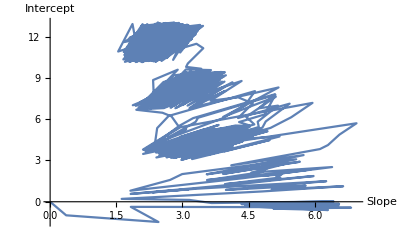

```mathematica
showPath[alldata, 25, 0.01]
```

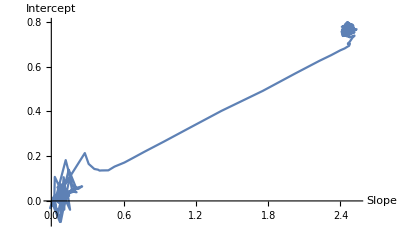

```mathematica
showPath[alldata, 25, 0.001]
```

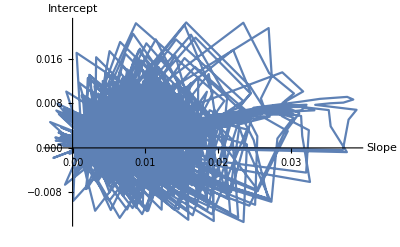

```mathematica
showPath[alldata, 25, 0.0001]
```

### Larger batches

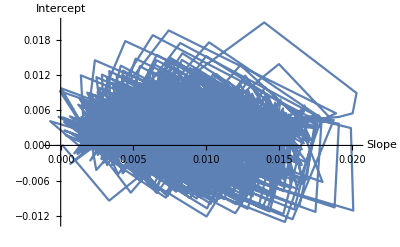

```mathematica
showPath[alldata,250, 0.0001]
```

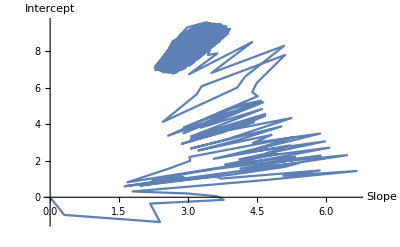

```mathematica
showPath[alldata, 250, 0.01]
```

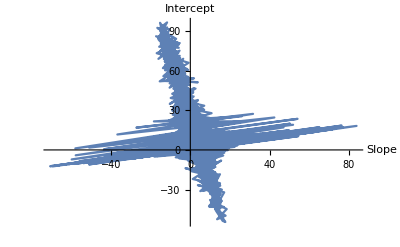

```mathematica
showPath[alldata, 250, 0.05]
```

### What happened with a big step size?

```mathematica
fakeloss[coef_]:=coef^2;
fakegradient[coef_]:=2*coef;
jump[coef_,stepsize_]:=-2*coef*stepsize;
(* nextPosition = x + jump; *)
```

```mathematica
ex=-4;
stepsize=0.1;
coefchain=NestList[#+jump[#, stepsize]&,ex,20];
Manipulate[
ex=coefchain[[step]];
Show[{Plot[fakeloss[x],{x,-4,4}],
Graphics[{Thick,Red,Arrow[{{ex,ex^2},{ex+jump[ex,stepsize], (ex^2)+(2*ex*jump[ex,stepsize])}}]}],
Graphics[
{Dashed,Red,Line[{{ex+jump[ex,stepsize], (ex^2)+(2*ex*jump[ex,stepsize])}, {ex+jump[ex,stepsize],0}}]}]},
PlotRange->All],
{step,1,Length[coefchain],1}];
```

## Problem 2: What’s perfect for our training set is not perfect for the underlying truth

```mathematica
polynomial[n_,x_]:=Subscript[coef, 0]+Total[(Subscript[coef, #1] x^#1&)/@Range[n]];
polynomial[7, x]
```

coef_0+x coef_1+x^2 coef_2+x^3 coef_3+x^4 coef_4+x^5 coef_5+x^6 coef_6+x^7 coef_7

```mathematica
optimalPolynomial[data_, n_]:=Module[
{f, error, coefs, optimal, minimized},
f=Function[{x}, polynomial[n, x]];
coefs= DeleteCases[Variables[f[x]], x];
{error, optimal}=Minimize[meanSquareError[f, data],coefs];
minimized[a_]:=f[a]/.optimal;
minimized
];
```

```mathematica
optimalPolynomial[train , 1][x]
optimalPolynomial[train , 3][x]
```

19.6614+0.89003 x

10.1655+7.35136 x-1.11928 x^2+0.0520354 x^3

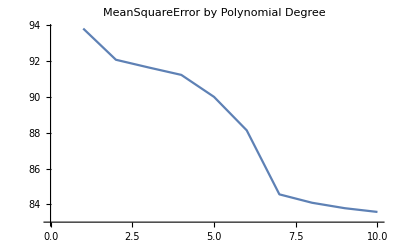

```mathematica
errors=Table[meanSquareError[optimalPolynomial[train , degrees], train],{degrees,10}];
ListLinePlot[errors, PlotLabel->"MeanSquareError by Polynomial Degree"]
```

```mathematica
Manipulate[Row[
{Labeled[plotFit[train, optimalPolynomial[train, n]], "Training Set"],
If[includeTest,Labeled[plotFit[test, optimalPolynomial[train, n]], "Test Set"]]}], 
{n,0,15,1}, {includeTest, {False, True}}];
```

### Bias: Underfitting, staying too close to base rates or means Variance: Overfitting, varying too much from each sample

```mathematica
biasvariance=Table[
train=RandomSample[ExampleData[{"MachineLearning", "BostonHomes"}, "TrainingData"], 100];
train={train[[All,1,8]],train[[All,2]]};
{meanSquareError[optimalPolynomial[train , 0], test],
meanSquareError[optimalPolynomial[train , 2], test],
meanSquareError[optimalPolynomial[train , 10], test]}
,10];
Column[biasvariance]
```

{82.1409,74.4737,81.667}
{80.7187,71.7075,73.0138}
{81.1271,70.1857,131.903}
{82.9773,74.3106,91.0926}
{81.4102,68.3392,270.767}
{80.9986,70.1733,21591.3}
{80.6555,70.7469,150470.}
{80.8619,71.3882,258.503}
{82.7111,72.6097,100.5}
{80.8569,71.8958,79.9533}

## Solution 2: Regularization and Cross Validation

#### L1 and L2 Regularization: Encourage using features less by adding penalties for larger coefficients

```mathematica
l1optimalPolynomial[data_, n_, l1_]:=Module[
{f, error, coefs, optimal, minimized, lossfunc},
f=Function[{x}, polynomial[n, x]];
coefs= DeleteCases[Variables[f[x]], x];
lossfunc = meanSquareError[f, data];
(* add a loss term for the Absolute value of each feature coefficient
i.e. not the first term which is the bias term *)
lossfunc = lossfunc + l1*Total[Rest[Abs[CoefficientList[coefs,x]]]];
{error, optimal}=Minimize[lossfunc,coefs];
minimized[a_]:=f[a]/.optimal;
minimized
];
```

```mathematica
optimalPolynomial[train,10][x]===l1optimalPolynomial[train,10,0][x]
```

```mathematica
Manipulate[Row[
{Labeled[plotFit[train, l1optimalPolynomial[train, n,l1penalty]], "Training Set"],
If[includeTest,Labeled[plotFit[test, l1optimalPolynomial[train, n,l1penalty]], "Test Set"]]}], 
{n,0,15,1}, {l1penalty, 0, 100, .05},{includeTest, {False, True}}];
```

```mathematica
Manipulate[Plot3D[bumpy+l1*Total[Abs[{slope,intercept}]],{slope,-5,10},{intercept,-10,10}],{l1,0,1000,0.05}];
```

```mathematica
Manipulate[Plot3D[bumpy+l2*Sqrt[Total[{slope,intercept}^2]],{slope,-5,10},{intercept,-10,10}],{l2,0,1000,0.05}];
```

## Cross Validation

### Repeatedly train on most of the training data, evaluate hyperparameters on the rest

### Automated Linear Predictor

```mathematica
predictor=Predict[homes, Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
Information[predictor]
```

Predictor information
Data type | Mixed (number: 13)
Standard deviation | 6.56 ± 1.2
Method | LinearRegression
Single evaluation time | 10. ms/example
Batch evaluation speed | 7.93 examples/ms
Loss | 3.32 ± 0.17
Model memory | 392. kB
Training examples used | 338 examples
Training time | 8.11 s
 |

### Automated Linear Classifier

```mathematica
higher=UnitStep[homes[[All,2]]-Median[homes[[All,2]]]]
```

{1,1,1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,1,0,1,1,1,0,0,1,1,1,0,0,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,1,1,0,0,0,1,0,1,0,0,1,1,1,1,0,0,0,1,0,0,0,0,1,1,0,1,0,1,0,0,0,1,1,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,1,1,0}

```mathematica
classifier=Classify[homes[[All,1]]->higher, Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
Information[classifier]
```

Classifier information
Data type | Mixed (number: 13)
Classes | ,,01
Accuracy | (87.72.8) %
Method | LogisticRegression
Single evaluation time | 9.55 ms/example
Batch evaluation speed | 13.3 examples/ms
Loss | 0.302 ± 0.056
Model memory | 411. kB
Training examples used | 338 examples
Training time | 12.5 s
 |

### Glimpse into Giulio’s lectures

```mathematica
fullPredictor[[1,"Model"]];
```

Part::partd: Part specification fullPredictor⟦1,Model⟧ is longer than depth of object.

```mathematica
classifier[[1,"Model"]]
```